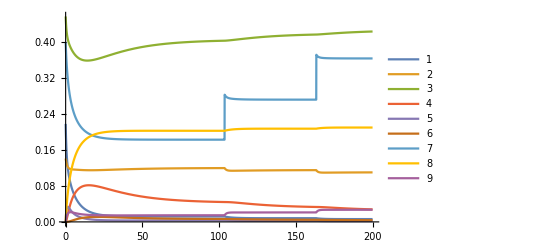

```mathematica
Clear["Global`*"];

des={x[1]'[t],x[2]'[t],x[3]'[t],x[4]'[t],x[5]'[t],x[6]'[t],x[7]'[t],x[8]'[t],x[9]'[t]}=={-k[1] x[1][t] x[3][t]+k[2] x[5][t]+k[3] x[5][t]-k[7] x[1][t] x[7][t]+k[8] x[8][t],-k[4] x[2][t] x[4][t]+k[5] x[6][t]+k[6] x[6][t]-k[9] x[2][t] x[7][t]+k[10] x[9][t],-k[1] x[1][t] x[3][t]+k[2] x[5][t]+k[6] x[6][t],-k[4] x[2][t] x[4][t]+k[3] x[5][t]+k[5] x[6][t],k[1] x[1][t] x[3][t]-k[2] x[5][t]-k[3] x[5][t],k[4] x[2][t] x[4][t]-k[5] x[6][t]-k[6] x[6][t],-k[7] x[1][t] x[7][t]-k[9] x[2][t] x[7][t]+k[8] x[8][t]+k[10] x[9][t],k[7] x[1][t] x[7][t]-k[8] x[8][t],k[9] x[2][t] x[7][t]-k[10] x[9][t]};

init={T[1],T[2],T[3],0,0,0,T[4],0,0};

vars=Array[x,9];
dvars=Thread[Derivative[1][vars]];

Block[{k,T,ssthreshold},k[n_]:=k[n]=(SeedRandom[n];RandomReal[]);
T[n_]:=T[n]=(SeedRandom[n+10];RandomReal[]);
ssthreshold=1.*^-4;
(*Print[des];*)(*to see the ODE*){sol}=NDSolve[{des,Through[vars[0]]==init,With[{df=Through[dvars[t]]},WhenEvent[Norm[df]<ssthreshold,x[7][t]->x[7][t]+0.1]]},vars,{t,0,200},MaxSteps->100000]];

Plot@@{Through[vars[t]]/.sol,Flatten@{t,x[1]["Domain"]/.sol},PlotLegends->Automatic}
```

## Analytical solution trial

```mathematica
solution=Solve[Table[0,{i,Length[des[[1]]]}]==des[[2]],Table[x[i][t],{i,Length[des[[1]]]}]]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{x[3][t]→((k[2]+k[3]) x[5][t])/(k[1] x[1][t]),x[4][t]→(k[3] (k[5]+k[6]) x[5][t])/(k[4] k[6] x[2][t]),x[6][t]→(k[3] x[5][t])/k[6],x[8][t]→(k[7] x[1][t] x[7][t])/k[8],x[9][t]→(k[9] x[2][t] x[7][t])/k[10]},{x[1][t]→0,x[4][t]→0,x[5][t]→0,x[6][t]→0,x[8][t]→0,x[9][t]→(k[9] x[2][t] x[7][t])/k[10]},{x[1][t]→0,x[2][t]→0,x[5][t]→0,x[6][t]→0,x[8][t]→0,x[9][t]→0},{x[2][t]→0,x[3][t]→0,x[5][t]→0,x[6][t]→0,x[8][t]→(k[7] x[1][t] x[7][t])/k[8],x[9][t]→0}}

```mathematica
(*Now we substitute several parameters*)
{(k[2]+k[3])/k[1]->km[1],(k[5]+k[6])/k[4]->km[2],k[3]/k[6]->kcr,k[7]/k[8]->kd[1],k[9]/k[10]->kd[2]}
```

```mathematica
newEqns={x[3][t]==(km[1]x[5][t])/(x[1][t]),x[4][t]==(kcr*km[2] x[5][t])/(x[2][t]),x[6][t]==kcr x[5][t],x[8][t]==kd[1] x[1][t] x[7][t],x[9][t]==kd[2] x[2][t] x[7][t],T[1]==x[1][t]+x[5][t]+x[8][t],T[2]==x[2][t]+x[6][t]+x[9][t],T[3]==x[3][t]+x[4][t]+x[5][t]+x[6][t],T[4]==x[7][t]+x[8][t]+x[9][t]}
```

{x[3][t]==(km[1] x[5][t])/(x[1][t]),x[4][t]==(kcr km[2] x[5][t])/(x[2][t]),x[6][t]==kcr x[5][t],x[8][t]==kd[1] x[1][t] x[7][t],x[9][t]==kd[2] x[2][t] x[7][t],T[1]==x[1][t]+x[5][t]+x[8][t],T[2]==x[2][t]+x[6][t]+x[9][t],T[3]==x[3][t]+x[4][t]+x[5][t]+x[6][t],T[4]==x[7][t]+x[8][t]+x[9][t]}